# ARAPdemo.nb (Ver.0.26) (Mathematica ARAP Modules 2017/02/04)

```mathematica
SetDirectory[FileNameJoin[{$HomeDirectory,"Desktop/git/MathematicaARAP/lib"}]];
<<ARAPlibv026.m;
<<ARAPdatav021.m;
```

## 1. Elementary Functions

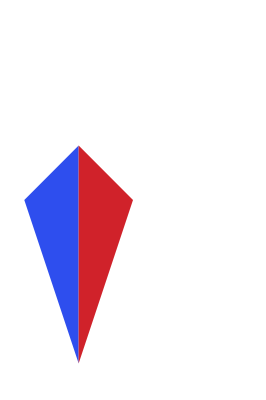
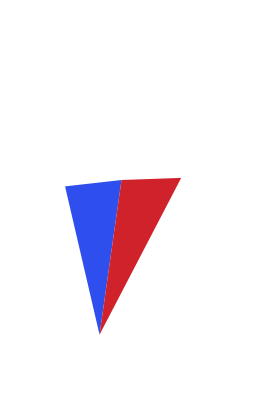
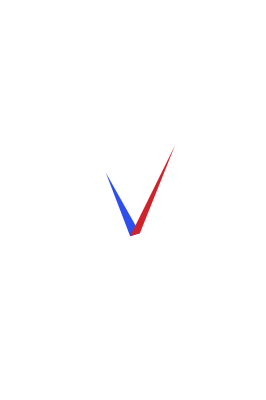
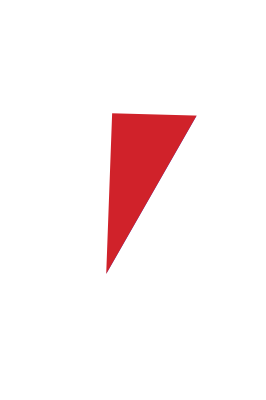
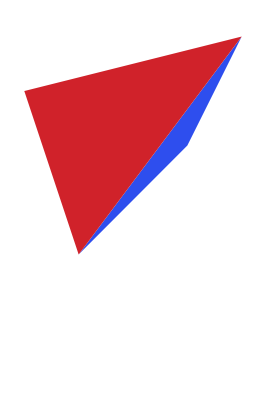

```mathematica
ListAnimation[5,LocalAlexa,QuadraticFormAlexa,ConstPair[1],Configuration2]
```

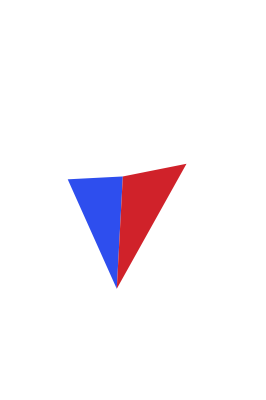
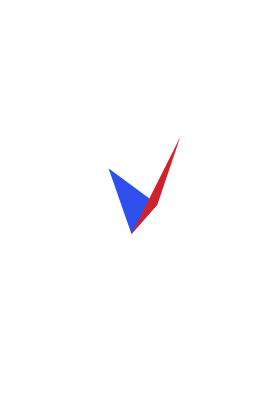
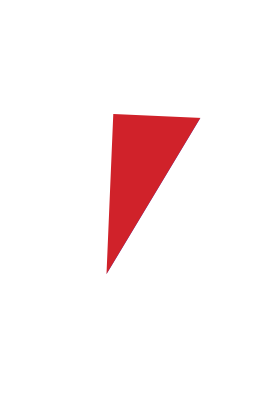
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListAnimation[5,LocalAlexa,QuadraticFormAlexa,ConstPair[1,2],Configuration2]
```

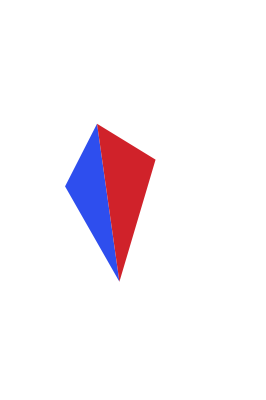
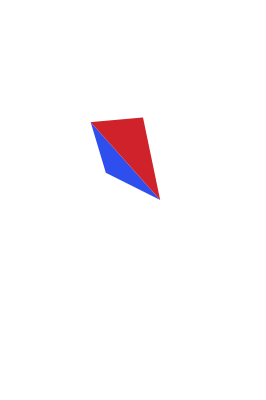
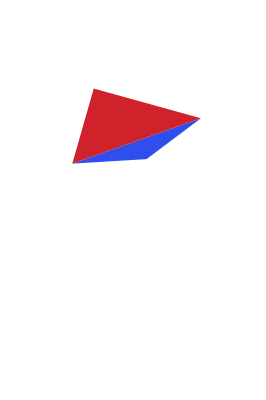
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListAnimation[5,LocalAlexa,QuadraticFormSim,ConstPair[1,2],Configuration2]
```

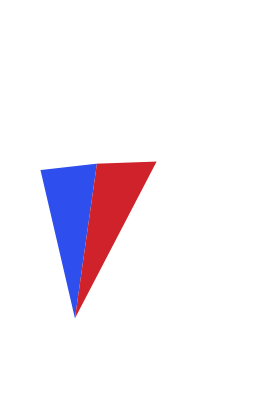
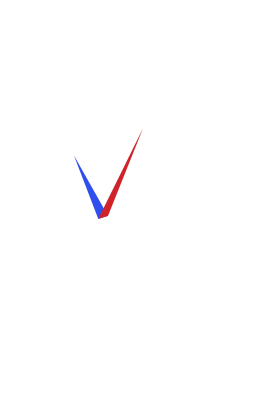
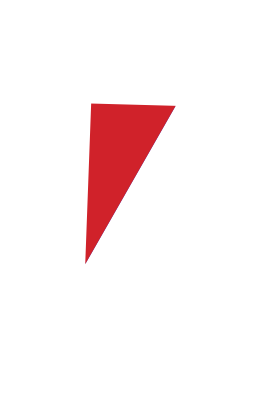
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListAnimation[5,LocalAlexa,QuadraticFormAlexa,ConstPairM,Configuration2]
```

```mathematica
DrawAnimation[LocalAlexa,QuadraticFormSim,ConstPair[1,2],Configuration2]
```

## 2. Energy Functions

### 2.1 Frobenius (Alexa) Energy

```mathematica
DrawAnimation[LocalAlexa,QuadraticFormAlexa,ConstPair[1],ConfigurationSnakeRotation]
```

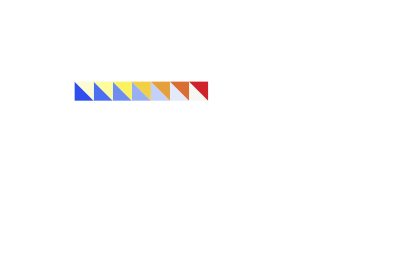
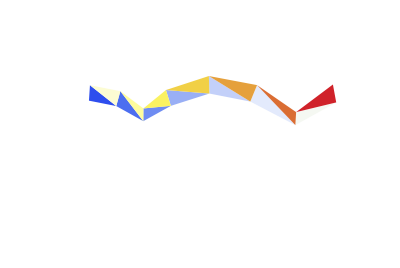
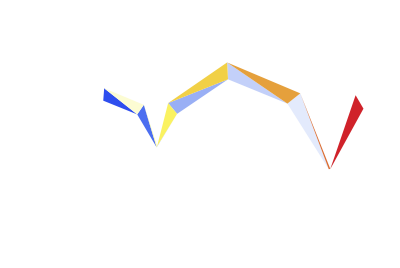
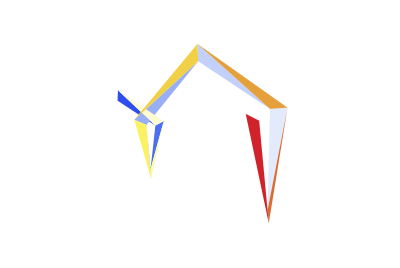
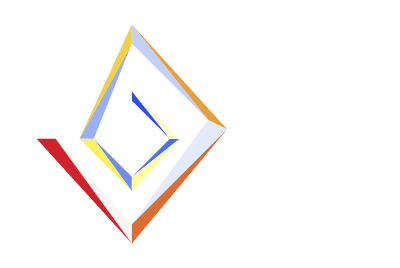

```mathematica
ListAnimation[5,LocalAlexa,QuadraticFormAlexa,ConstPair[1],ConfigurationSnakeRotation]
```

### 2.1 Sim Energy

```mathematica
DrawAnimation[LocalAlexa,QuadraticFormSim,ConstPair[1,2],ConfigurationSnakeRotation]
```

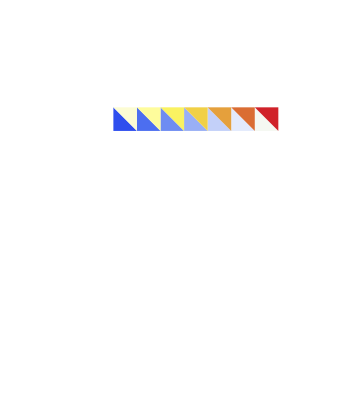
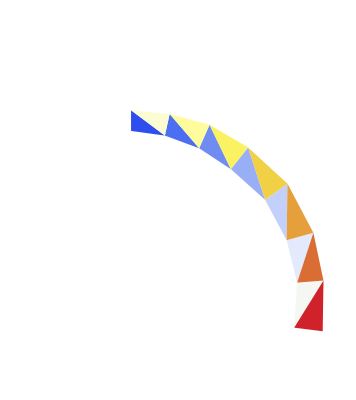
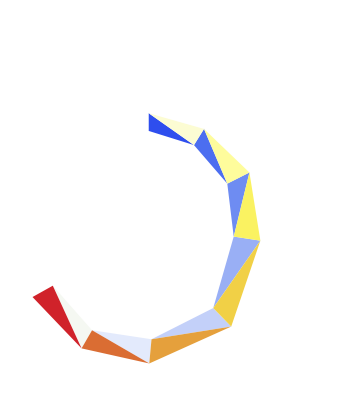
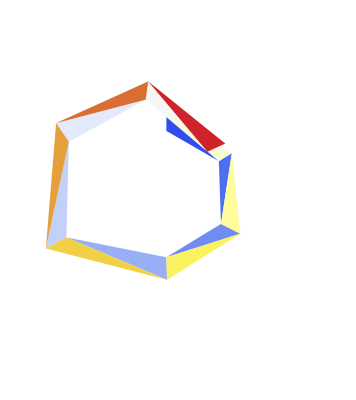
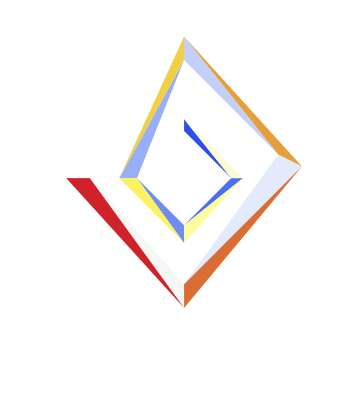

```mathematica
ListAnimation[5,LocalLogExp,QuadraticFormSim,ConstPair[1,2],ConfigurationSnakeRotation]
```

## 3. Constraint Functions

### 3.1 1 point constraint

```mathematica
DrawAnimation[LocalAlexa,QuadraticFormAlexa,ConstPair[1],ConfigurationVN]
```

```mathematica
ListAnimation[30,LocalAlexa,QuadraticFormAlexa,ConstPair[1],ConfigurationVN];
```

### 3.2 2 point constraint

```mathematica
DrawAnimation[LocalLogExp,QuadraticFormSim,ConstPair[1,2],ConfigurationVN]
```

```mathematica
ListAnimation[30,LocalLogExp,QuadraticFormSim,ConstPair[1,2],ConfigurationVN];
```

## 4. Compiled Functions

```mathematica
Timing[ListAnimation[10,LocalAlexa,QuadraticFormAlexa,ConstPair[1],ConfigurationVN]]//First
```

0.147022

CompiledFunction::cfse: コンパイルされた式{{1.,0.},{0.,1.}}はmachine-size real numberであるべきです．

CompiledFunction::cfex: 命令20の外部評価を完了することができませんでした．コンパイルなしで評価を続行します．

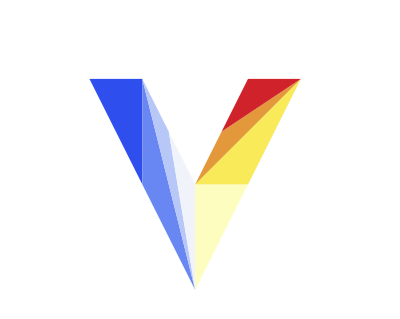
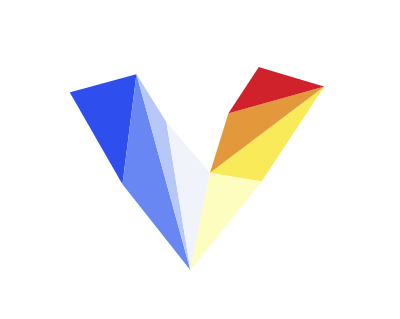
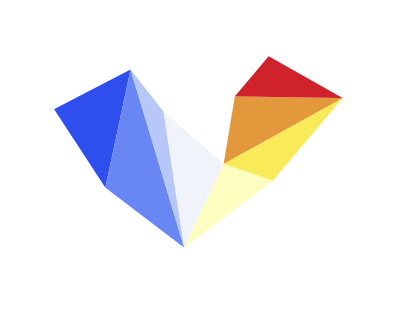
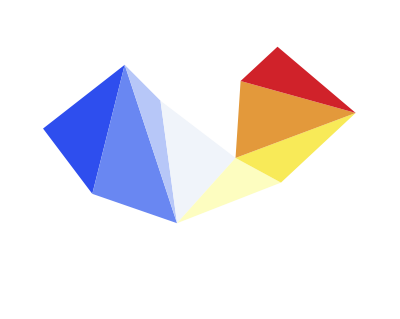
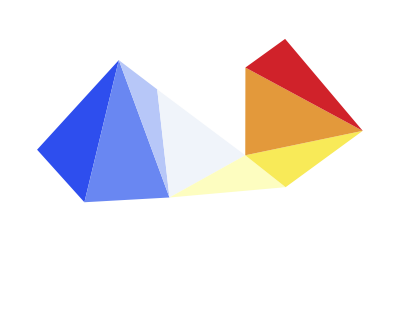
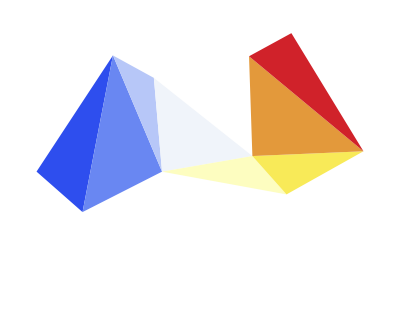
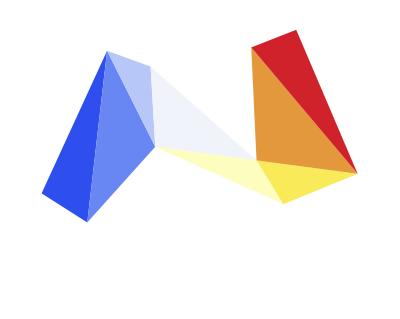
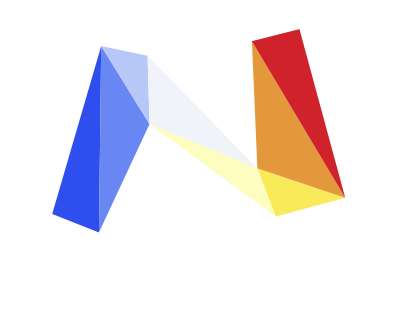
{0.099739,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Timing[cListAnimation[10,ConfigurationVN]]
```

CompiledFunction::cfse: コンパイルされた式{{1.,0.},{0.,1.}}はmachine-size real numberであるべきです．

CompiledFunction::cfex: 命令20の外部評価を完了することができませんでした．コンパイルなしで評価を続行します．

Inverse::luc: 行列{{55171.6,0.,-23117.6,0.,0.,0.,0.,0.,-11480.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-15124.6,0.,0.,0.,0.,0.,-5447.96,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2160»},«49»,«2160»}に含まれる悪条件より，Inverseの結果には重大な数値誤差が含まれている可能性があります．

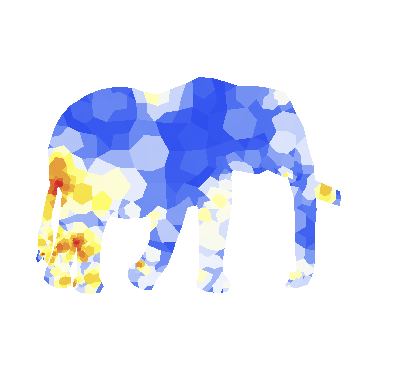
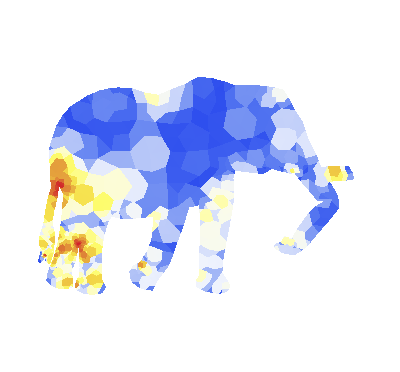
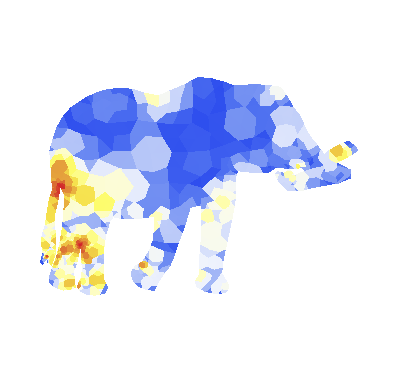
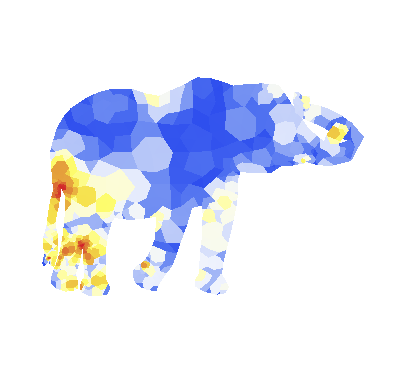
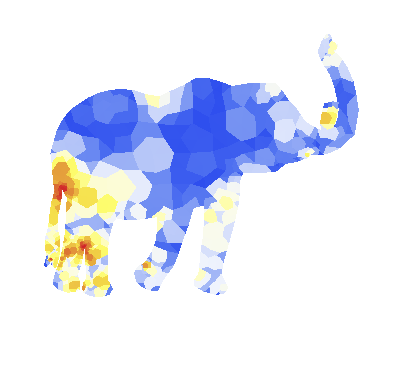
{16.2977,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Timing[cListAnimation[5,ConfigurationElephant]]
```

```mathematica
cDrawAnimation[5,ConfigurationElephant]
```

CompiledFunction::cfse: コンパイルされた式{{1.,0.},{0.,1.}}はmachine-size real numberであるべきです．

CompiledFunction::cfex: 命令20の外部評価を完了することができませんでした．コンパイルなしで評価を続行します．

Inverse::luc: 行列{{55171.6,0.,-23117.6,0.,0.,0.,0.,0.,-11480.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-15124.6,0.,0.,0.,0.,0.,-5447.96,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2160»},«49»,«2160»}に含まれる悪条件より，Inverseの結果には重大な数値誤差が含まれている可能性があります．

CompiledFunction::cfse: コンパイルされた式{{1.,0.},{0.,1.}}はmachine-size real numberであるべきです．

CompiledFunction::cfex: 命令16の外部評価を完了することができませんでした．コンパイルなしで評価を続行します．

CompiledFunction::cfse: コンパイルされた式{{0.999933,-0.012656},{0.0126833,0.999913}}はmachine-size real numberであるべきです．

General::stop: この計算中に，CompiledFunction::cfseのこれ以上の出力は表示されません．

CompiledFunction::cfex: 命令16の外部評価を完了することができませんでした．コンパイルなしで評価を続行します．

General::stop: この計算中に，CompiledFunction::cfexのこれ以上の出力は表示されません．

## 5. Verification of correctness of precomputed functions

### 5.1 Verification of F1a

```mathematica
Module[{A,B},A=({{Subscript[m, 11], Subscript[m, 12]}, {Subscript[m, 21], Subscript[m, 22]}}); B=(({{Subscript[v, 1x], Subscript[v, 2x], Subscript[v, 3x]}, {Subscript[v, 1y], Subscript[v, 2y], Subscript[v, 3y]}, {1, 1, 1}}).Inverse[({{Subscript[a, x], Subscript[b, x], Subscript[c, x]}, {Subscript[a, y], Subscript[b, y], Subscript[c, y]}, {1, 1, 1}})])[[1;;2,1;;2]];
F1a[{{Subscript[a, x],Subscript[a, y]},{Subscript[b, x],Subscript[b, y]},{Subscript[c, x],Subscript[c, y]}},A]==
QuadraticFormMatrix[NormF[B-A],{Subscript[v, 1x],Subscript[v, 2x],Subscript[v, 3x],Subscript[v, 1y],Subscript[v, 2y],Subscript[v, 3y]}][[1;;3,1;;3]]//FullSimplify]
```

True

### 5.2 Verification of F2a

```mathematica
Module[{A,B},
A=({{Subscript[m, 11], Subscript[m, 12]}, {Subscript[m, 21], Subscript[m, 22]}}); B=(({{Subscript[v, 1x], Subscript[v, 2x], Subscript[v, 3x]}, {Subscript[v, 1y], Subscript[v, 2y], Subscript[v, 3y]}, {1, 1, 1}}).Inverse[({{Subscript[a, x], Subscript[b, x], Subscript[c, x]}, {Subscript[a, y], Subscript[b, y], Subscript[c, y]}, {1, 1, 1}})])[[1;;2,1;;2]];
F2a[{{Subscript[a, x],Subscript[a, y]},{Subscript[b, x],Subscript[b, y]},{Subscript[c, x],Subscript[c, y]}},A]==
QuadraticFormMatrix[
NormF[B]-(NormF[B.Transpose[A]]+2 Det[B.Transpose[A]])/NormF[A],{Subscript[v, 1x],Subscript[v, 1y],Subscript[v, 2x],Subscript[v, 2y],Subscript[v, 3x],Subscript[v, 3y]}]]//FullSimplify
```

True